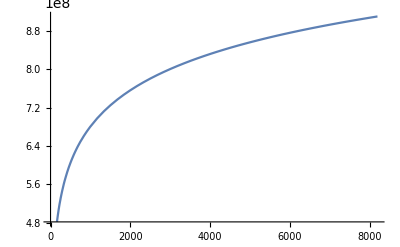

```mathematica
screenViewDist=QuantityMagnitude[UnitConvert@Quantity[20.0,"Inches"],"Meters"];
screenDiag=QuantityMagnitude[UnitConvert@Quantity[13.3,"Inches"],"Meters"];
screenRes= {1920,1080}/10;
maxViewDist=2^13;(*horizon*)

maxPixelsPerM=Sqrt[(Norm[screenRes]/screenDiag)^2*screenViewDist^2];
voxelScaleFactor[m_]:=m^-3;
(*8^-Log2[m]*)
averageDensity=1;
voxelDensity[m_]:=voxelScaleFactor[m]*averageDensity*maxPixelsPerM^3;
Log2@CubeRoot[voxelDensity[1]];
totalNumVoxels[maxViewDist_]:=Sum[voxelDensity[d](d^3-(d-1)^3),{d,maxViewDist}];
maxNmVoxels=totalNumVoxels[maxViewDist];
Plot[totalNumVoxels[k],{k,0,maxViewDist}]
```

```mathematica
voxelDatasize=Quantity[4.*2203800,"Bytes"]/((1024^3))
voxelDatasize*maxNmVoxels
totalSize=UnitConvert[%,"Gb"]
```

0.00820979 B

7.47059×10^6 B

0.0597647 Gb

```mathematica
size=2^13;
bytePerVoxel=4;
maxResolution=2^5;
blockSize=2^1;

averageLayerFill=0.45;
ClearAll[totalMemory]
logisticalBytes=4;

totalMemory[0]:=bytePerVoxel*blockSize^3;
totalMemory[layer_]:=1+8(logisticalBytes+bytePerVoxel+averageLayerFill*totalMemory[layer-1]);

numLevels=Ceiling@Log2[size*maxResolution/blockSize]
totalMemory[numLevels]/2^30
```

17

152.096

```mathematica
avgFill=Table[
img =DiskMatrix[1/2{2,2,2}^level,2^level];
cmeans=Total/@Flatten[Partition[img,{2,2,2}],{{1,2,3},{4,5,6}}];
Mean[4-Abs[4-cmeans]]//N,
{level,1,8}]
```

{0.,1.,1.625,0.53125,0.328125,0.166504,0.0849915,0.0423203}

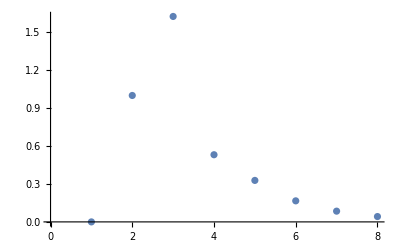

```mathematica
ListPlot[{0.,1.,1.625,0.53125,0.328125,0.16650390625,0.084991455078125,0.04232025146484375}]
```

```mathematica
Array
```